## T1 transition

```mathematica
sortCC[polyinds_]:=Block[{cent,poly},
poly=Lookup[indToPtsAssoc,polyinds];
Lookup[ptsToIndAssoc,
DeleteDuplicates@Flatten[MeshPrimitives[ConvexHullMesh[poly],1]/.Line->Sequence,1]
]
];

sortPointCC[polyPoints_]:=Block[{cent,ordering},
cent=Mean@polyPoints;
ordering=Ordering[ArcTan[#[[1]],#[[2]]]&@(#-cent)&/@polyPoints];
Part[polyPoints,ordering]
];
```

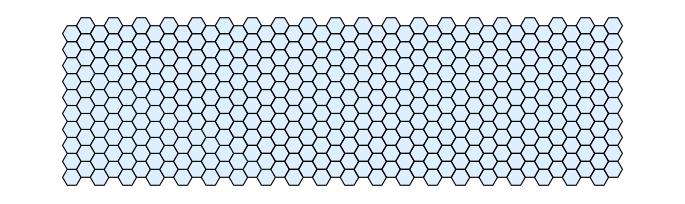

```mathematica
hexTile[n_,m_]:=With[{hex=Polygon[Table[{Cos[2 Pi k/6]+#,Sin[2 Pi k/6]+#2},{k,6}]]&},Table[hex[3 i+3 ((-1)^j+1)/4,Sqrt[3]/2 j],{i,n},{j,m}]];
Graphics[{EdgeForm[Black],LightBlue,hexTile[20,20]}]
```

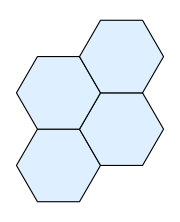

```mathematica
plt=First[hexTile[1,4]]//Map[{EdgeForm[Black],LightBlue,#}&,#]&//Graphics[#,ImageSize->Small]&
```

```mathematica
mesh=First[hexTile[1,4]]
```

{Polygon[…],Polygon[…],Polygon[…],Polygon[…]}

```mathematica
pts=Replace[MeshPrimitives[#,0]&/@mesh,Point[x:{__Real}]:> x,{2}];
```

```mathematica
ptsToIndAssoc=AssociationThread[#-> Range[Length@#]]&@DeleteDuplicates@Flatten[pts,1];
```

```mathematica
indToPtsAssoc=AssociationMap[Reverse,ptsToIndAssoc];
```

```mathematica
(* let us do T1 about point 5 and 10 *)
```

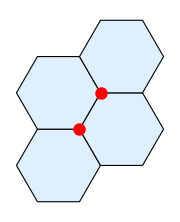

```mathematica
Show[plt,Graphics[{Red,PointSize[0.05],Point@indToPtsAssoc[#]&/@{5,10}}],ImageSize->Small]
```

```mathematica
edge={indToPtsAssoc[5],indToPtsAssoc[10]};
```

```mathematica
edgeindex=ptsToIndAssoc/@edge;
```

```mathematica
ptindices=Map[Lookup[ptsToIndAssoc,#]&,pts];
```

```mathematica
cellindices=AssociationThread[Range[4]-> ptindices];
```

```mathematica
keyscells=Keys@cellindices;
```

```mathematica
pos=Position[Values@Normal@cellindices,{OrderlessPatternSequence[___,5,___,10,___]},{1}];//AbsoluteTiming
```

{0.0000426,Null}

```mathematica
midpoint=Midpoint[edge];
```

```mathematica
(* take the vertex and rotate anticlockwise *)
```

```mathematica
dsep=0.2;
```

```mathematica
newpts=midpoint+dsep Normalize[(#-midpoint)]&/@Flatten[RotationTransform[-π/2,midpoint]/@{edge},1];
```

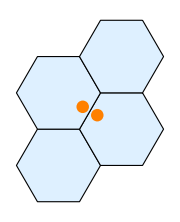

```mathematica
Show[plt,Graphics[{Orange,PointSize[0.05],Point@newpts}],ImageSize-> Small]
```

```mathematica
memF=Function[x,RegionMember@x,Listable][Extract[mesh,pos]];
```

```mathematica
pp=Extract[keyscells,pos];
```

```mathematica
selkeys=Thread[pp->memF]
```

{2→                                  3 Sqrt[3]       3 Sqrt[3]    7                Sqrt[3]       Sqrt[3]    11
RegionMemberFunction[Polygon[{{5, ---------}, {4, ---------}, {-, Sqrt[3]}, {4, -------}, {5, -------}, {--, Sqrt[3]}}], <>]
                                      2               2        2                   2             2       2,3→                               7               5                  3 Sqrt[3]    5             7                3 Sqrt[3]
RegionMemberFunction[Polygon[{{-, 2 Sqrt[3]}, {-, 2 Sqrt[3]}, {2, ---------}, {-, Sqrt[3]}, {-, Sqrt[3]}, {4, ---------}}], <>]
                               2               2                      2        2             2                    2}

```mathematica
xx=#->First@@Select[selkeys,Function[x,Last[x][#]]]&/@newpts (*pt to cell *)
```

{{3.57679,2.26506}→3,{3.92321,2.06506}→2}

```mathematica
newptsindices=Range[#+1,#+2]&[Max[Keys@indToPtsAssoc]]
```

{17,18}

```mathematica
AppendTo[indToPtsAssoc,Thread[newptsindices->newpts]];
```

```mathematica
AppendTo[ptsToIndAssoc,Thread[newpts->newptsindices]];
```

```mathematica
yy=MapAt[ptsToIndAssoc,xx,{All,1}]/.Rule->List (*index to cell*)
```

{{17,3},{18,2}}

```mathematica
keysToMap=MapAt[Key,yy,{All,2}]
```

{{17,Key[3]},{18,Key[2]}}

```mathematica
zz=Fold[MapAt[Function[x,DeleteDuplicates[x/.Thread[{5,10}->#2[[1]]]]],#1,#2[[2]]]&,cellindices,keysToMap]
```

<|1→{1,2,3,4,5,6},2→{18,4,7,8,9},3→{11,6,17,12,13},4→{12,10,9,14,15,16}|>

```mathematica
otherkeys=List@*Key/@Complement[keyscells,pp]
```

{{Key[1]},{Key[4]}}

```mathematica
oo=MapAt[(#/.(Alternatives@@edgeindex)->Splice[newptsindices]//sortCC)&,zz,otherkeys]
```

<|1→{1,2,3,4,18,17,6},2→{18,4,7,8,9},3→{11,6,17,12,13},4→{12,17,18,9,14,15,16}|>

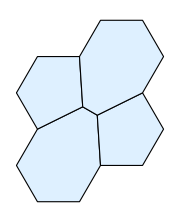

```mathematica
Graphics[{EdgeForm[{Black}],LightBlue,Values[Polygon@Lookup[indToPtsAssoc,#]&/@oo]},ImageSize->Small]
```

```mathematica
points=Lookup[indToPtsAssoc,#]&/@Lookup[oo,{1,4}];
```

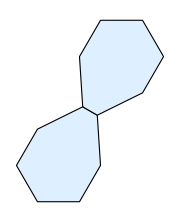

```mathematica
Polygon@sortPointCC[#]&/@points//Graphics[{EdgeForm[{Thick,Black}],LightBlue,#},ImageSize->Small]&
```